```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/juanathan/Documentos/Wolfram Mathematica/Wolfram_scripts

```mathematica
<<"GradientDescend.wls"
```

```mathematica
f = (#1-5)^2 + #2^2 &;
df = {2*(#1-5),  2*#2}&
var = {x,y};
x0 = {-8,-8};
```

{2 (#1-5),2 #2}&

```mathematica
BarzilaiBorwein[df,{{0,1},{0.1,+1.1}}]
BarzilaiBorwein[df[x,y],{x,y},{{0,1},{0.1,+1.1}}]
```

0.5

0.5

```mathematica
GradientDescent[f[x,y],{var,x0}]
GradientDescent[f,df,x0]

GradientDescent[f[x,y],{var,x0}, Tolerance -> .01]
GradientDescent[f,df,x0,Tolerance -> .01]

GradientDescent[f[x,y],{var,x0}, LearningRate -> .001]
GradientDescent[f,df,x0,LearningRate -> .01]

GradientDescent[f[x,y],{var,x0}, LearningRate -> .01, Tolerance-> 0.01]
GradientDescent[f,df,x0,LearningRate -> .001, Tolerance-> 0.01]

GradientDescent[f[x,y],{var,x0},LearningRate -> "Barzilai-Borwein"]
GradientDescent[f,df,x0,LearningRate -> "Barzilai-Borwein"]
```

{{4.99959,-0.000252071},2.31487×10^-7}

{{4.99959,-0.000252071},2.31487×10^-7}

{{4.58954,-0.252468},0.232215}

{{4.58954,-0.252468},0.232215}

{{3.24551,-1.07917},4.24283}

{{4.99959,-0.000252071},2.31487×10^-7}

{{4.58954,-0.252468},0.232215}

{{0.757892,-2.60927},24.8038}

{{5.,0.},0.}

{{5.,0.},0.}

```mathematica
NGradientDescent[f,x0]
NGradientDescent[f,x0,Tolerance -> .01]
NGradientDescent[f,x0, LearningRate -> .01]
NGradientDescent[f,x0, "Step" -> .01]
NGradientDescent[f,x0,LearningRate -> .0001, Tolerance-> 0.00001,"Step" -> .00000001,MaxIterations->1000000]
NGradientDescent[f,x0,LearningRate -> "Barzilai-Borwein"]
```

{{4.99653,-0.0021743},0.0000167849}

{{4.96849,-0.0194184},0.00136981}

{{4.95888,-0.0253332},0.00233295}

{{4.98663,-0.0120717},0.000324478}

{{4.95742,-0.0261899},0.00249889}

{{4.9999,-0.0001},2.×10^-8}

```mathematica
NGradientDescent[f[x,y],var,x0]
NGradientDescent[f[x,y],var,x0,Tolerance -> .01]
NGradientDescent[f[x,y],var,x0, LearningRate -> .01]
NGradientDescent[f[x,y],var,x0, "Step" -> .01]
NGradientDescent[f[x,y],var,x0,LearningRate -> .0001, Tolerance-> 0.00001,"Step" -> .00000001,MaxIterations->1000000]
NGradientDescent[f[x,y],var,x0,LearningRate -> "Barzilai-Borwein"]
```

{{4.99653,-0.0021743},0.0000167849}

{{4.96849,-0.0194184},0.00136981}

{{4.95888,-0.0253332},0.00233295}

{{4.98663,-0.0120717},0.000324478}

{{4.95742,-0.0261899},0.00249889}

{{4.9999,-0.0001},2.×10^-8}

{{-7.88465,2.88763},87.6026}

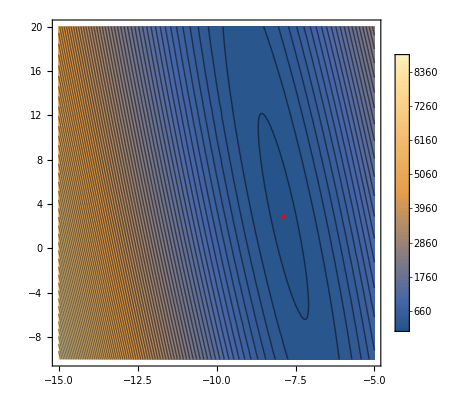

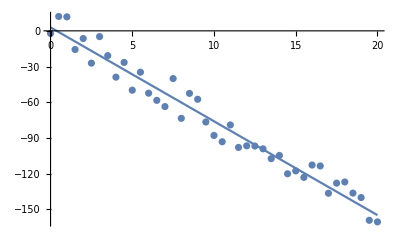

```mathematica
equis = Range[0,20,.5];
data = -8 equis + 5 + RandomReal[{-3,3}*5,Length[equis]];

error = Plus @@ (((#1 equis + #2)-data)^2)/Length[equis] &;
NGradientDescent[error,{-5,-5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5]
fitParameters = %[[1]];
ContourPlot[error[m,b],{m,-15,-5},{b,-10,20},Contours->80,PlotLegends->Automatic,Epilog->{Red,Point[fitParameters]}]
Show[{ListPlot[data,DataRange->equis[[{1,-1}]]],
Plot[m*x+b /.Thread[{m,b}->fitParameters],{x,equis[[1]],equis[[-1]]}]}]
```

{{-8.8415,3.5266,-160.12},8303.36}

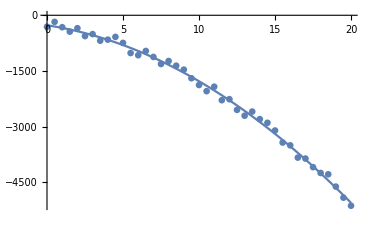

```mathematica
equis = Range[0,20,.5];
data = -8 (equis + 5)^2 + 3 + RandomReal[{-3,3}*50,Length[equis]];

error = Plus @@ (((#1 (equis + #2)^2 + #3)-data)^2)/Length[equis] &;
NGradientDescent[error,{-5,-5,-5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5]
fitParameters = %[[1]];
Show[{ListPlot[data,DataRange->equis[[{1,-1}]]],
Plot[a ( x + b)^2 + c /.Thread[{a,b,c}->fitParameters],{x,equis[[1]],equis[[-1]]}]}]
```